```mathematica
sinTwsq=0.23
alpha=1.25
sigma0=1.76*10^(-44)
Csn=(1+5*alpha^2)/24
Csp=(4*(Cv-1)^2+5*alpha^2)/24
Cv=1/2+2*sinTwsq
sigmaSN=CsN*sigma0*(Ev/(me*c^2))^2
Ev=kb*T/Sqrt[(5/(7*Pi^2))]
Ksn=Csn*sigma0*(Ev/(me*c^2))^2/mn
Ksp=Csp*sigma0*(Ev/(me*c^2))^2/mp
```

0.23

1.25

1.76×10^-44

0.367188

0.325788

0.96

5.46508×10^-31 CsN

5.13231×10^-16 T

1.51625×10^-39 T^2

1.34715×10^-39 T^2

```mathematica
Ev/(kb*T)
```

3.71718

```mathematica
Sqrt[1/(5/(7*Pi^2.))]
```

3.71718

```mathematica
Yn=1-Yp
tausn=rho/mb*Yn*mn*Ksn*H//.{rho->rho10*10^(10),T->T11*10^11}
tausp=rho/mb*Yp*mp*Ksp*H//.{rho->rho10*10^(10),T->T11*10^11}
taustot=tausn+tausp
fstaustot=FullSimplify[taustot/(1.51729*10^(-7))]
```

1-Yp

1.51729×10^-7 H rho10 T11^2 (1-Yp)

1.34622×10^-7 H rho10 T11^2 Yp

1.51729×10^-7 H rho10 T11^2 (1-Yp)+1.34622×10^-7 H rho10 T11^2 Yp

H rho10 T11^2 (1.-0.112749 Yp)

```mathematica
fstaustot//.{Yp->0.5}
```

0.943627 H rho10 T11^2

```mathematica
taustotfake=(tausn//.{Yn->1})+(tausp//.{Yp->1})
```

2.86351×10^-7 H rho10 T11^2

```mathematica
FullSimplify[taustot/(1.71073*10^(-8))]
```

H rho10 T11^2 (8.86927-1. Yp)

```mathematica
taustot//.{Yp->1/2}
```

1.43176×10^-7 H rho10 T11^2

```mathematica
tausn//.{Yp->1.0}
tausp//.{Yp->1.0}
taustot//.{Yp->0.5}
```

0. H rho10 T11^2

1.34622×10^-7 H rho10 T11^2

1.43176×10^-7 H rho10 T11^2

1.51729×10^-7 (1-Yp)+1.34622×10^-7 Yp

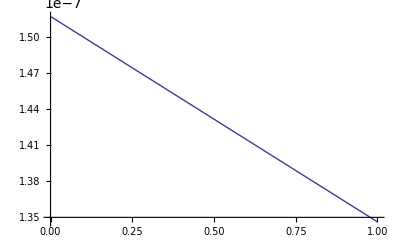

```mathematica
toplot=taustot//.{H->1,T11->1,rho10->1}
Plot[toplot,{Yp,0,1}]
```

```mathematica
(* Burrows *)
```

```mathematica
Kb=10^(-20)*(Ev/ergPmev)^2
tau=Kb*rho*H//.{rho->rho10*10^(10),T->T11*10^11}
```

1.02614×10^-39 T^2

1.02614×10^-7 H rho10 T11^2

```mathematica
KbA=3*10^(-20)*(Ev/ergPmev)^2*(A/56)
tauA=KbA*rho*H//.{rho->rho10*10^(10),T->T11*10^11}
```

5.49717×10^-41 A T^2

5.49717×10^-9 A H rho10 T11^2

```mathematica
tauA*56
```

3.07841×10^-7 A H rho10 T11^2

```mathematica
tau*3/56*28
```

1.53921×10^-7 H rho10 T11^2

```mathematica
(* Shapiro, page 526 *)
```

```mathematica
(* scattering per bound nuclei with atomic mass A *)
```

```mathematica
sigmaAcoh=1/16*sigma0*(Ev/(me*c^2))^2*A^2*(1-Z/A+(4*sinTwsq-1)*Z/A)^2
KbAcoh=sigmaAcoh/(A*amu)
tauAcoh=KbAcoh*rho*H//.{rho->rho10*10^(10),T->T11*10^11}
```

4.32273×10^-64 A^2 T^2 (1-(1.08 Z)/A)^2

2.60321×10^-40 A T^2 (1-(1.08 Z)/A)^2

2.60321×10^-8 A H rho10 T11^2 (1-(1.08 Z)/A)^2

```mathematica
tauAcoh*56
```

1.4578×10^-6 A H rho10 T11^2 (1-(1.08 Z)/A)^2

```mathematica
tauAcoh*56//.{Z->0.5*A}
```

3.0847×10^-7 A H rho10 T11^2

```mathematica
tauAcoh*56//.{Z->0.0*A}
```

1.4578×10^-6 A H rho10 T11^2

```mathematica
(* look at Shapiro's free nucleon scattering *)
```

```mathematica
sigman=1/4*sigma0*(Ev/(me*c^2))^2
kappan=sigman/mb
taun=kappan*rho*H
```

1.72909×10^-63 T^2

1.03305×10^-39 T^2

1.03305×10^-39 H rho T^2

```mathematica
taun//.{rho->rho10*10^(10),T->T11*10^11}
```

1.03305×10^-7 H rho10 T11^2

```mathematica
(* equation 18.4.7 for energy of neutrino *)
```

```mathematica
Evshapiro=51.6*(Ye*rho/10^(12))^(1/3)
```

0.00516 (rho Ye)^(1/3)

```mathematica
Enulimit=300*A^(-1/3)
```

300/A^(1/3)

```mathematica
Enulimit//.{A->56.}
```

78.4137